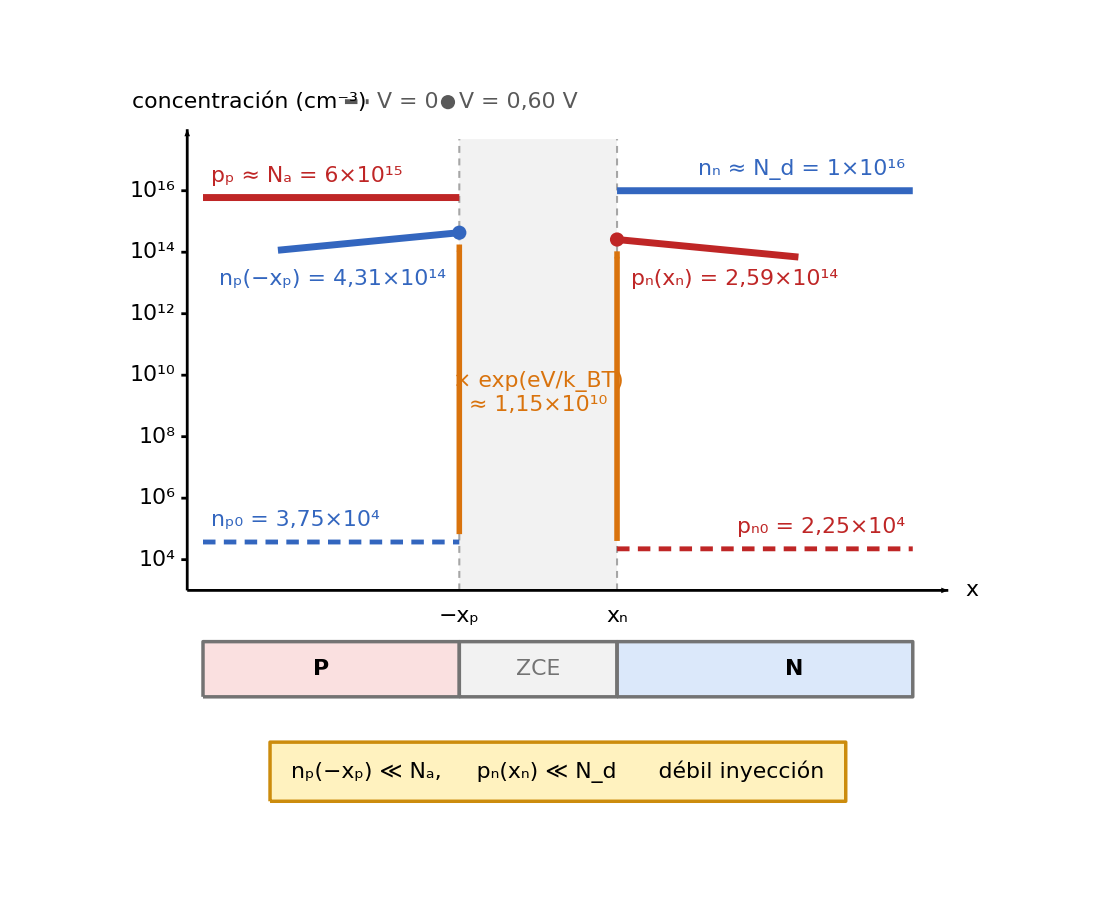

```mathematica
diagramaMinoritarios = Module[
  {fs, mostrarValores, Wz, Ldec, cAzul, cAzulB, cRojo, cRojoF, cNar, cGris, cOro, cOroB,
   Nac, Ndc, ni, Vap, kT, np0, pn0, fac, npB, pnB, xp, xn, cx, y0, sy, X, yl,
   ins, insI, insD, flecha, caja, cient, val, curvaN, curvaP},

  (* ---------- Parámetros globales ---------- *)
  fs = 22;                 (* tamaño de fuente único para todo el gráfico *)
  mostrarValores = True;   (* False oculta los valores numéricos *)
  cAzul = RGBColor[0.86, 0.91, 0.98];  cAzulB = RGBColor[0.20, 0.40, 0.75];
  cRojo = RGBColor[0.75, 0.15, 0.15];  cRojoF = RGBColor[0.98, 0.88, 0.88];
  cNar  = RGBColor[0.85, 0.45, 0.05];  cGris  = GrayLevel[0.45];
  cOro  = RGBColor[1.0, 0.95, 0.75];   cOroB  = RGBColor[0.80, 0.55, 0.05];

  (* ---------- Datos del ejemplo (cm^-3, V) ---------- *)
  Nac = 6.*10.^15;  Ndc = 10.^16;  ni = 1.5*10.^10;  Vap = 0.60;  kT = 0.0259;
  np0 = ni^2/Nac;  pn0 = ni^2/Ndc;       (* minoritarios en equilibrio *)
  fac = Exp[Vap/kT];                     (* factor de Boltzmann *)
  npB = np0 fac;  pnB = pn0 fac;         (* n_p(-x_p) y p_n(x_n) *)

  (* ---------- Geometría ---------- *)
  Wz = 4.0;                      (* anchura total de la ZCE (esquemática) *)
  Ldec = 3.5;                    (* longitud de decaimiento del dibujo (esquemática) *)
  xp = Wz Ndc/(Nac + Ndc);       (* la ZCE penetra más en el lado menos dopado (P) *)
  xn = Wz Nac/(Nac + Ndc);
  cx = 12.8;  y0 = 6.0;  sy = 0.78;
  X[u_] := cx + u;
  yl[c_] := y0 + sy (Log10[c] - 3);      (* eje vertical logarítmico *)

  (* ---------- Funciones auxiliares ---------- *)
  ins[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos];
  insI[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Left, Center}];
  insD[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Right, Center}];
  flecha[p1_, p2_, col_] :=
    {col, AbsoluteThickness[4], Arrowheads[0.02], Arrow[{p1, p2}]};
  caja[{xc_, yc_}, {w_, h_}, relleno_, borde_] :=
    {EdgeForm[{AbsoluteThickness[2.5], borde}], relleno,
     Rectangle[{xc - w/2, yc - h/2}, {xc + w/2, yc + h/2}, RoundingRadius -> 0.15]};
  cient[x_] := Module[{ex = Floor[Log10[x]], m},
    m = Round[x/10.^ex, 0.01];
    Row[{If[m == Round[m], Round[m], NumberForm[m, {3, 2}, NumberPoint -> ","]],
      "×", Superscript["10", ex]}]];
  val[x_] := If[mostrarValores, Row[{" = ", cient[x]}], ""];

  (* decaimiento cualitativo desde cada borde hacia el equilibrio *)
  curvaN = Table[{X[-xp - d], yl[np0 + (npB - np0) Exp[-d/Ldec]]}, {d, 0., 4.6, 0.1}];
  curvaP = Table[{X[xn + d], yl[pn0 + (pnB - pn0) Exp[-d/Ldec]]}, {d, 0., 4.6, 0.1}];

  (* ---------- Diagrama ---------- *)
  Graphics[{
    (* ZCE: banda y bordes *)
    {GrayLevel[0.95], EdgeForm[None], Rectangle[{X[-xp], y0}, {X[xn], 17.45}]},
    {GrayLevel[0.65], AbsoluteThickness[1.5], AbsoluteDashing[{5, 4}],
     Line[{{X[-xp], y0}, {X[-xp], 17.45}}], Line[{{X[xn], y0}, {X[xn], 17.45}}]},

    (* ejes del gráfico logarítmico *)
    {Black, AbsoluteThickness[2], Arrowheads[0.02],
     Arrow[{{X[-9.4], y0}, {X[9.9], y0}}], Arrow[{{X[-9.4], y0}, {X[-9.4], 17.7}}]},
    ins[Style["x", Italic], {X[10.5], y0}],
    insI[Row[{"concentración (", Superscript["cm", "−3"], ")"}], {X[-10.8], 18.4}],
    Table[{Black, AbsoluteThickness[2],
      Line[{{X[-9.55], yl[10.^k]}, {X[-9.4], yl[10.^k]}}],
      insD[Row[{Superscript["10", k]}], {X[-9.7], yl[10.^k]}]}, {k, 4, 16, 2}],
    ins[Row[{"−", Subscript["x", "p"]}], {X[-xp], 5.35}],
    ins[Row[{Subscript["x", "n"]}], {X[xn], 5.35}],

    (* leyenda: equilibrio (discontinua) y polarización directa (punto) *)
    {GrayLevel[0.35], AbsoluteThickness[3.5], AbsoluteDashing[{9, 6}],
     Line[{{X[-5.4], 18.4}, {X[-4.8], 18.4}}]},
    insI[Row[{Style["V", Italic], " = 0"}], {X[-4.6], 18.4}, GrayLevel[0.35]],
    {GrayLevel[0.35], Disk[{X[-2.8], 18.4}, 0.18]},
    insI[If[mostrarValores,
      Row[{Style["V", Italic], " = ", NumberForm[Vap, {2, 2}, NumberPoint -> ","], " V"}],
      Row[{Style["V", Italic], " > 0"}]], {X[-2.5], 18.4}, GrayLevel[0.35]],

    (* minoritarios en equilibrio *)
    {cAzulB, AbsoluteThickness[3.5], AbsoluteDashing[{9, 6}],
     Line[{{X[-9], yl[np0]}, {X[-xp], yl[np0]}}]},
    {cRojo, AbsoluteThickness[3.5], AbsoluteDashing[{9, 6}],
     Line[{{X[xn], yl[pn0]}, {X[9], yl[pn0]}}]},
    insI[Row[{Subscript["n", "p0"], val[np0]}], {X[-8.8], yl[np0] + 0.55}, cAzulB],
    insD[Row[{Subscript["p", "n0"], val[pn0]}], {X[8.8], yl[pn0] + 0.55}, cRojo],

    (* mayoritarios *)
    {cRojo, AbsoluteThickness[5], Line[{{X[-9], yl[Nac]}, {X[-xp], yl[Nac]}}]},
    {cAzulB, AbsoluteThickness[5], Line[{{X[xn], yl[Ndc]}, {X[9], yl[Ndc]}}]},
    insI[Row[{Subscript["p", "p"], " ≈ ", Subscript["N", "a"], val[Nac]}],
     {X[-8.8], yl[Nac] + 0.55}, cRojo],
    insD[Row[{Subscript["n", "n"], " ≈ ", Subscript["N", "d"], val[Ndc]}],
     {X[8.8], yl[Ndc] + 0.55}, cAzulB],

    (* minoritarios en los bordes de la ZCE con polarización directa *)
    {cAzulB, AbsoluteThickness[5], Arrowheads[0.02], Arrow[curvaN]},
    {cRojo, AbsoluteThickness[5], Arrowheads[0.02], Arrow[curvaP]},
    {cAzulB, Disk[{X[-xp], yl[npB]}, 0.18]},
    {cRojo, Disk[{X[xn], yl[pnB]}, 0.18]},
    insD[Row[{Subscript["n", "p"], "(−", Subscript["x", "p"], ")", val[npB]}],
     {X[-xp] - 0.35, 13.9}, cAzulB],
    insI[Row[{Subscript["p", "n"], "(", Subscript["x", "n"], ")", val[pnB]}],
     {X[xn] + 0.35, 13.9}, cRojo],

    (* aumento de los minoritarios respecto al equilibrio *)
    flecha[{X[-xp], yl[np0] + 0.2}, {X[-xp], yl[npB] - 0.3}, cNar],
    flecha[{X[xn], yl[pn0] + 0.2}, {X[xn], yl[pnB] - 0.3}, cNar],
    ins[Column[{
       Row[{"× exp(", Style["e", Italic], Style["V", Italic], "/",
         Subscript["k", "B"], Style["T", Italic], ")"}],
       If[mostrarValores, Row[{"≈ ", cient[fac]}], ""]}, Center],
     {X[(xn - xp)/2], 11.0}, cNar],

    (* tira P | ZCE | N alineada con el gráfico *)
    {cRojoF, EdgeForm[{AbsoluteThickness[2.5], cGris}],
     Rectangle[{X[-9], 3.3}, {X[-xp], 4.7}]},
    {cAzul, EdgeForm[{AbsoluteThickness[2.5], cGris}],
     Rectangle[{X[xn], 3.3}, {X[9], 4.7}]},
    {GrayLevel[0.95], EdgeForm[{AbsoluteThickness[2.5], cGris, AbsoluteDashing[{7, 5}]}],
     Rectangle[{X[-xp], 3.3}, {X[xn], 4.7}]},
    ins[Style["P", Bold], {X[-6], 4.0}],
    ins[Style["N", Bold], {X[6], 4.0}],
    ins["ZCE", {X[(xn - xp)/2], 4.0}, cGris],

    (* débil inyección *)
    caja[{cx, 1.4}, {14.6, 1.5}, cOro, cOroB],
    ins[Row[{Subscript["n", "p"], "(−", Subscript["x", "p"], ") ≪ ",
       Subscript["N", "a"], ",     ", Subscript["p", "n"], "(", Subscript["x", "n"],
       ") ≪ ", Subscript["N", "d"], "      débil inyección"}], {cx, 1.4}]
   },
   ImageSize -> 1100,
   PlotRange -> {{1.2, 24.0}, {0.3, 18.9}},
   PlotRangePadding -> None,
   AspectRatio -> 18.6/22.8,
   Background -> White]
];
diagramaMinoritarios
```

```mathematica
Export[CloudObject["T4_E1.png"], diagramaMinoritarios, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 800]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T4_E1.png]

```mathematica
diagramaJsaturacion = Module[
  {fs, mostrarValores, Wz, cAzul, cAzulB, cRojo, cRojoF, cVio, cNar, cGris, cOro, cOroB,
   e, ni, Nac, Ndc, Dn, Dp, tau, Aar, np0, pn0, Ln, Lp, Jn, Jp, Jsat, Isat,
   cx, y0, hv, Lnd, Lpd, hN, hP, xp, xn, hJ, hn, hp, xb0, xb1, X,
   ins, insI, insD, flecha, caja, carga, cient, eq, ap, curvaN, curvaP},

  (* ---------- Parámetros globales ---------- *)
  fs = 22;                 (* tamaño de fuente único para todo el gráfico *)
  mostrarValores = True;   (* False oculta los valores numéricos *)
  cAzul = RGBColor[0.86, 0.91, 0.98];  cAzulB = RGBColor[0.20, 0.40, 0.75];
  cRojo = RGBColor[0.75, 0.15, 0.15];  cRojoF = RGBColor[0.98, 0.88, 0.88];
  cVio  = RGBColor[0.45, 0.25, 0.65];  cNar   = RGBColor[0.85, 0.45, 0.05];
  cGris = GrayLevel[0.45];
  cOro  = RGBColor[1.0, 0.95, 0.75];   cOroB  = RGBColor[0.80, 0.55, 0.05];

  (* ---------- Datos del ejemplo (cm, s, A) ---------- *)
  e = 1.6*10^-19;  ni = 1.5*10.^10;  Nac = 10.^16;  Ndc = 10.^16;
  Dn = 25.;  Dp = 10.;  tau = 5.*10^-7;  Aar = 10.^-4;
  np0 = ni^2/Nac;  pn0 = ni^2/Ndc;           (* minoritarios en equilibrio *)
  Ln = Sqrt[Dn tau];  Lp = Sqrt[Dp tau];     (* longitudes de difusión *)
  Jn = e Dn np0/Ln;  Jp = e Dp pn0/Lp;
  Jsat = Jn + Jp;  Isat = Jsat Aar;

  (* ---------- Geometría ---------- *)
  Wz = 2.4;                                  (* anchura de la ZCE en el dibujo (no a escala) *)
  xp = Wz Ndc/(Nac + Ndc);  xn = Wz Nac/(Nac + Ndc);
  cx = 9.2;  y0 = 4.6;  hv = 4.4;
  Lnd = 2.2;  Lpd = Lnd Lp/Ln;               (* L_n y L_p del dibujo, en proporción real *)
  hN = hv np0/Max[np0, pn0];  hP = hv pn0/Max[np0, pn0];
  hJ = 4.8;  hn = hJ Jn/Jsat;  hp = hJ Jp/Jsat;
  {xb0, xb1} = {19.3, 20.9};
  X[u_] := cx + u;

  (* ---------- Funciones auxiliares ---------- *)
  ins[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos];
  insI[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Left, Center}];
  insD[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Right, Center}];
  flecha[p1_, p2_, col_, s_: 0.022] :=
    {col, AbsoluteThickness[4], Arrowheads[s], Arrow[{p1, p2}]};
  caja[{xc_, yc_}, {w_, h_}, relleno_, borde_] :=
    {EdgeForm[{AbsoluteThickness[2.5], borde}], relleno,
     Rectangle[{xc - w/2, yc - h/2}, {xc + w/2, yc + h/2}, RoundingRadius -> 0.15]};
  carga[pos_, signo_, col_] :=
    {col, Disk[pos, 0.33], Text[Style[signo, Round[0.95 fs], Bold, White], pos]};
  cient[x_] := Module[{ex = Floor[Log10[x]], m},
    m = Round[x/10.^ex, 0.01];
    Row[{If[m == Round[m], Round[m], NumberForm[m, {3, 2}, NumberPoint -> ","]],
      "×", Superscript["10", ex]}]];
  eq[x_] := If[mostrarValores, Row[{" = ", cient[x]}], ""];
  ap[x_, u_] := If[mostrarValores, Row[{" ≈ ", cient[x], " ", u}], ""];

  (* perfiles: se anulan en el borde de la ZCE y tienden al equilibrio *)
  curvaN = Table[{X[-xp - d], y0 + hN (1 - Exp[-d/Lnd])}, {d, 0., 6.8, 0.1}];
  curvaP = Table[{X[xn + d], y0 + hP (1 - Exp[-d/Lpd])}, {d, 0., 6.8, 0.1}];

  (* ---------- Diagrama ---------- *)
  Graphics[{
    (* ===== Unión en polarización inversa ===== *)
    {cRojoF, EdgeForm[{AbsoluteThickness[2.5], cGris}],
     Rectangle[{X[-7.6], 11.6}, {X[-xp], 13.8}]},
    {cAzul, EdgeForm[{AbsoluteThickness[2.5], cGris}],
     Rectangle[{X[xn], 11.6}, {X[7.6], 13.8}]},
    {GrayLevel[0.95], EdgeForm[{AbsoluteThickness[2.5], cGris, AbsoluteDashing[{7, 5}]}],
     Rectangle[{X[-xp], 11.6}, {X[xn], 13.8}]},
    ins[Style["P", Bold], {X[-6.8], 12.7}],
    ins[Style["N", Bold], {X[6.8], 12.7}],
    carga[{X[-5.2], 12.7}, "−", cAzulB],
    carga[{X[-3.9], 12.7}, "−", cAzulB],
    flecha[{X[-3.3], 12.7}, {X[-1.75], 12.7}, cAzulB, 0.014],
    carga[{X[5.2], 12.7}, "+", cRojo],
    carga[{X[3.9], 12.7}, "+", cRojo],
    flecha[{X[3.3], 12.7}, {X[1.75], 12.7}, cRojo, 0.014],
    flecha[{X[xn - 0.2], 12.45}, {X[-xp + 0.2], 12.45}, cVio, 0.014],
    ins[Row[{OverVector["E"]}], {cx, 13.25}, cVio],
    ins["ZCE", {cx, 11.15}, cGris],
    ins["electrones minoritarios", {X[-4.4], 14.35}, cAzulB],
    ins["huecos minoritarios", {X[4.4], 14.35}, cRojo],
    ins[Row[{"polarización inversa  (", Style["V", Italic], " < 0)"}], {cx, 15.1}, cGris],

    (* ===== Perfil de los minoritarios ===== *)
    {GrayLevel[0.95], EdgeForm[None], Rectangle[{X[-xp], y0}, {X[xn], y0 + 5.6}]},
    {GrayLevel[0.65], AbsoluteThickness[1.5], AbsoluteDashing[{5, 4}],
     Line[{{X[-xp], 11.6}, {X[-xp], y0}}], Line[{{X[xn], 11.6}, {X[xn], y0}}]},
    {Black, AbsoluteThickness[2], Arrowheads[0.02],
     Arrow[{{X[-8.2], y0}, {X[8.2], y0}}], Arrow[{{X[-8.2], y0}, {X[-8.2], y0 + 5.6}}]},
    ins[Style["x", Italic], {X[8.8], y0}],
    insD["0", {X[-8.45], y0}],
    insI[Row[{"concentración (", Superscript["cm", "−3"], ")"}], {X[-8.4], 10.9}],
    ins[Row[{"−", Subscript["x", "p"]}], {X[-xp], y0 - 0.45}],
    ins[Row[{Subscript["x", "n"]}], {X[xn], y0 - 0.45}],

    (* concentraciones de equilibrio *)
    {cAzulB, AbsoluteThickness[3.5], AbsoluteDashing[{9, 6}],
     Line[{{X[-xp], y0 + hN}, {X[-8.0], y0 + hN}}]},
    {cRojo, AbsoluteThickness[3.5], AbsoluteDashing[{9, 6}],
     Line[{{X[xn], y0 + hP}, {X[8.0], y0 + hP}}]},
    insI[Row[{Subscript["n", "p0"], eq[np0]}], {X[-7.9], y0 + hN + 0.5}, cAzulB],
    insD[Row[{Subscript["p", "n0"], eq[pn0]}], {X[7.9], y0 + hP + 0.5}, cRojo],

    (* pendiente en los bordes: la tangente corta la meseta a la distancia L *)
    {cNar, AbsoluteThickness[3], AbsoluteDashing[{6, 4}],
     Line[{{X[-xp], y0}, {X[-xp - Lnd], y0 + hN}}],
     Line[{{X[xn], y0}, {X[xn + Lpd], y0 + hP}}]},
    {GrayLevel[0.6], AbsoluteThickness[1.5], AbsoluteDashing[{3, 4}],
     Line[{{X[-xp - Lnd], y0 + hN}, {X[-xp - Lnd], y0 - 1.0}}],
     Line[{{X[xn + Lpd], y0 + hP}, {X[xn + Lpd], y0 - 1.0}}]},

    (* perfiles de los minoritarios *)
    {cAzulB, AbsoluteThickness[5], Line[curvaN]},
    {cRojo, AbsoluteThickness[5], Line[curvaP]},
    ins[Row[{Subscript["n", "p"], "(", Style["x", Italic], ")"}],
     {X[-xp - 3.6], y0 + 1.9}, cAzulB],
    ins[Row[{Subscript["p", "n"], "(", Style["x", Italic], ")"}],
     {X[xn + 2.6], y0 + 1.9}, cRojo],

    (* longitudes de difusión *)
    {Black, AbsoluteThickness[2], Arrowheads[{-0.012, 0.012}],
     Arrow[{{X[-xp], y0 - 0.9}, {X[-xp - Lnd], y0 - 0.9}}],
     Arrow[{{X[xn], y0 - 0.9}, {X[xn + Lpd], y0 - 0.9}}]},
    ins[Row[{Subscript["L", "n"],
       If[mostrarValores, Row[{" ≈ ", Round[Ln 10^4], " μm"}], ""]}],
     {X[-xp - Lnd/2], y0 - 1.55}],
    ins[Row[{Subscript["L", "p"],
       If[mostrarValores, Row[{" ≈ ", Round[Lp 10^4], " μm"}], ""]}],
     {X[xn + Lpd/2], y0 - 1.55}],

    (* ===== Contribuciones a la densidad de corriente ===== *)
    {EdgeForm[{AbsoluteThickness[2.5], cAzulB}], cAzul,
     Rectangle[{xb0, y0}, {xb1, y0 + hn}]},
    {EdgeForm[{AbsoluteThickness[2.5], cRojo}], cRojoF,
     Rectangle[{xb0, y0 + hn}, {xb1, y0 + hn + hp}]},
    ins[Row[{Subscript["J", "n"]}], {(xb0 + xb1)/2, y0 + hn/2}, cAzulB],
    ins[Row[{Subscript["J", "p"]}], {(xb0 + xb1)/2, y0 + hn + hp/2}, cRojo],
    {Black, AbsoluteThickness[2], Arrowheads[{-0.012, 0.012}],
     Arrow[{{21.4, y0}, {21.4, y0 + hJ}}]},
    insI[Row[{Subscript["J", "s"]}], {21.7, y0 + hJ/2}],
    If[mostrarValores,
     {ins[Row[{Subscript["J", "n"], " ≈ ", cient[Jn]}], {20.3, y0 - 0.8}, cAzulB],
      ins[Row[{Subscript["J", "p"], " ≈ ", cient[Jp]}], {20.3, y0 - 1.55}, cRojo],
      ins[Row[{"A/", Superscript["cm", 2]}], {20.3, y0 - 2.3}, cGris]},
     {}],

    (* ===== Resultado ===== *)
    caja[{cx, 1.2}, {12.8, 2.1}, cOro, cOroB],
    ins[Column[{
       Row[{Subscript["J", "s"], " = ", Subscript["J", "n"], " + ", Subscript["J", "p"],
         ap[Jsat, Row[{"A/", Superscript["cm", 2]}]]}],
       Row[{Subscript["I", "s"], " = ", Subscript["J", "s"], Style["A", Italic],
         If[mostrarValores,
          Row[{" ≈ ", cient[Isat], " A   (", Style["A", Italic], " = ",
            cient[Aar], " ", Superscript["cm", 2], ")"}], ""]}]}, Center], {cx, 1.2}]
   },
   ImageSize -> 1100,
   PlotRange -> {{0, 23.2}, {-0.1, 15.6}},
   PlotRangePadding -> None,
   AspectRatio -> 15.7/23.2,
   Background -> White]
];
diagramaJsaturacion
```

-Graphics-

```mathematica
Export[CloudObject["T4_E2.png"], diagramaJsaturacion, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 800]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T4_E2.png]

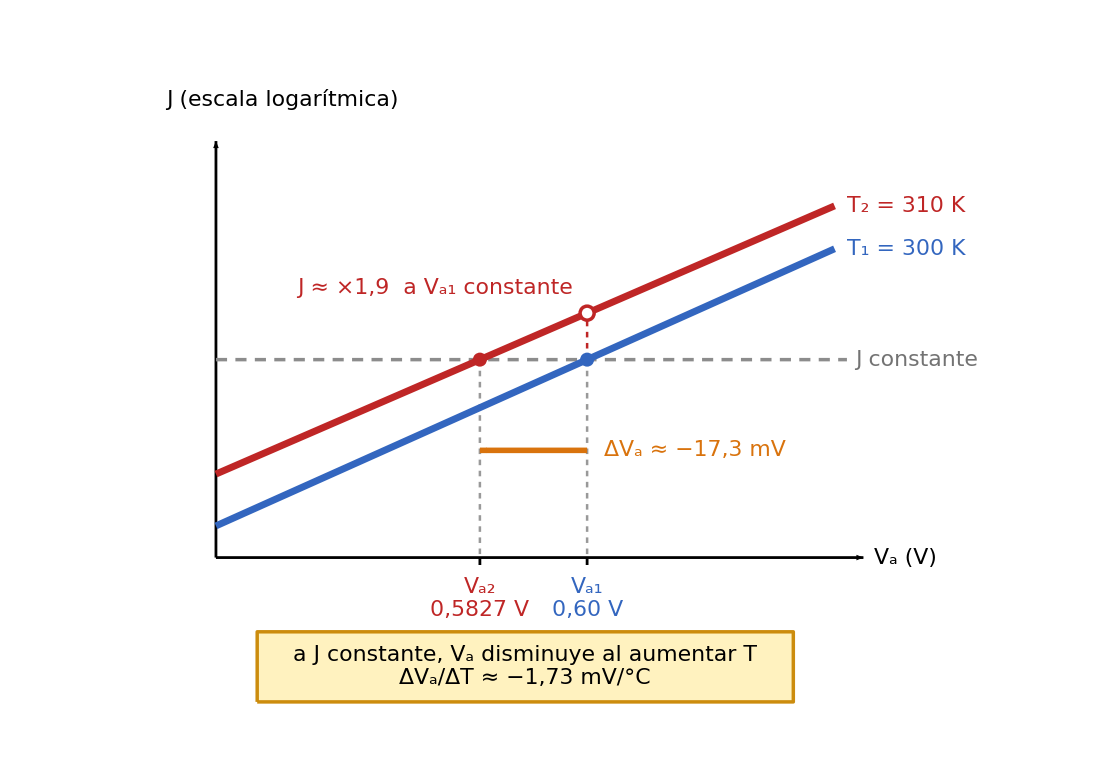

```mathematica
diagramaVdirTemperatura = Module[
  {fs, mostrarValores, cAzulB, cRojo, cNar, cGris, cOro, cOroB,
   kB, T1, T2, Eg, V1, V2, dV, coef, kT1, kT2, lJ1, lJ2, ratio,
   ox, oy, sx, sy, vmin, vmax, xV, yL, ins, insI, flecha, caja, dec, neg},

  (* ---------- Parámetros globales ---------- *)
  fs = 22;                 (* tamaño de fuente único para todo el gráfico *)
  mostrarValores = True;   (* False oculta los valores numéricos *)
  cAzulB = RGBColor[0.20, 0.40, 0.75];  cRojo = RGBColor[0.75, 0.15, 0.15];
  cNar   = RGBColor[0.85, 0.45, 0.05];  cGris = GrayLevel[0.45];
  cOro   = RGBColor[1.0, 0.95, 0.75];   cOroB = RGBColor[0.80, 0.55, 0.05];

  (* ---------- Datos del ejemplo (eV, V, K) ---------- *)
  kB = 8.617*10^-5;  T1 = 300.;  T2 = 310.;  Eg = 1.12;  V1 = 0.60;
  kT1 = kB T1;  kT2 = kB T2;
  V2 = Eg - (Eg - V1) T2/T1;          (* tensión que mantiene la corriente constante *)
  dV = V2 - V1;  coef = dV/(T2 - T1);
  (* log10 de J relativo a la corriente en (V1, T1): J ∝ exp[-(Eg - eV)/(kB T)] *)
  lJ1[v_] := (v - V1)/(kT1 Log[10]);
  lJ2[v_] := (v - Eg)/(kT2 Log[10]) - (V1 - Eg)/(kT1 Log[10]);
  ratio = 10^lJ2[V1];                 (* J2/J1 a tensión constante V1 *)

  (* ---------- Geometría ---------- *)
  {ox, oy} = {3.0, 3.6};              (* origen de los ejes *)
  {sx, sy} = {150., 4.0};             (* unidades de dibujo por voltio y por década *)
  {vmin, vmax} = {0.54, 0.64};
  xV[v_] := ox + sx (v - vmin);
  yL[l_] := oy + sy (l + 1.2);

  (* ---------- Funciones auxiliares ---------- *)
  ins[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos];
  insI[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Left, Center}];
  insD[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Right, Center}];
  flecha[p1_, p2_, col_] :=
    {col, AbsoluteThickness[4], Arrowheads[0.022], Arrow[{p1, p2}]};
  caja[{xc_, yc_}, {w_, h_}, relleno_, borde_] :=
    {EdgeForm[{AbsoluteThickness[2.5], borde}], relleno,
     Rectangle[{xc - w/2, yc - h/2}, {xc + w/2, yc + h/2}, RoundingRadius -> 0.15]};
  dec[x_, k_] := NumberForm[x, {5, k}, NumberPoint -> ","];
  neg[x_, k_] := Row[{"−", NumberForm[Abs[x], {5, k}, NumberPoint -> ","]}];

  (* ---------- Diagrama ---------- *)
  Graphics[{
    (* ejes *)
    {Black, AbsoluteThickness[2], Arrowheads[0.02],
     Arrow[{{ox, oy}, {xV[vmax] + 0.7, oy}}], Arrow[{{ox, oy}, {ox, yL[1.2] + 0.5}}]},
    insI[Row[{Subscript["V", "a"], " (V)"}], {xV[vmax] + 0.95, oy}],
    ins[Row[{Style["J", Italic], " (escala logarítmica)"}], {ox + 1.6, yL[1.2] + 1.5}],

    (* corriente constante *)
    {GrayLevel[0.55], AbsoluteThickness[2.5], AbsoluteDashing[{8, 6}],
     Line[{{ox, yL[0]}, {xV[vmax] + 0.3, yL[0]}}]},
    insI[Row[{Style["J", Italic], " constante"}], {xV[vmax] + 0.5, yL[0]}, cGris],

    (* guías hacia el eje de tensión y hacia la curva de T2 *)
    {GrayLevel[0.6], AbsoluteThickness[1.8], AbsoluteDashing[{4, 4}],
     Line[{{xV[V1], yL[0]}, {xV[V1], oy}}], Line[{{xV[V2], yL[0]}, {xV[V2], oy}}]},
    {cRojo, AbsoluteThickness[1.8], AbsoluteDashing[{4, 4}],
     Line[{{xV[V1], yL[0]}, {xV[V1], yL[lJ2[V1]]}}]},
    Table[{Black, AbsoluteThickness[2], Line[{{xV[v], oy}, {xV[v], oy - 0.18}}]},
     {v, {V1, V2}}],
    ins[Column[{Row[{Subscript["V", "a2"]}],
       If[mostrarValores, Row[{dec[V2, 4], " V"}], ""]}, Center],
     {xV[V2], oy - 1.0}, cRojo],
    ins[Column[{Row[{Subscript["V", "a1"]}],
       If[mostrarValores, Row[{dec[V1, 2], " V"}], ""]}, Center],
     {xV[V1], oy - 1.0}, cAzulB],

    (* curvas a T1 y T2 *)
    {cAzulB, AbsoluteThickness[5],
     Line[{{xV[vmin], yL[lJ1[vmin]]}, {xV[vmax], yL[lJ1[vmax]]}}]},
    {cRojo, AbsoluteThickness[5],
     Line[{{xV[vmin], yL[lJ2[vmin]]}, {xV[vmax], yL[lJ2[vmax]]}}]},
    insI[Row[{Subscript["T", 1], " = ", Round[T1], " K"}],
     {xV[vmax] + 0.3, yL[lJ1[vmax]]}, cAzulB],
    insI[Row[{Subscript["T", 2], " = ", Round[T2], " K"}],
     {xV[vmax] + 0.3, yL[lJ2[vmax]]}, cRojo],

    (* puntos de corriente constante y efecto a tensión constante *)
    {cAzulB, Disk[{xV[V1], yL[0]}, 0.17]},
    {cRojo, Disk[{xV[V2], yL[0]}, 0.17]},
    {White, Disk[{xV[V1], yL[lJ2[V1]]}, 0.17], cRojo, AbsoluteThickness[2.5],
     Circle[{xV[V1], yL[lJ2[V1]]}, 0.17]},
    insD[Row[{Style["J", Italic],
       If[mostrarValores,
        Row[{" ≈ ×", NumberForm[ratio, {3, 1}, NumberPoint -> ","]}],
        " aumenta"],
       "  a ", Subscript["V", "a1"], " constante"}],
     {xV[V1] - 0.35, yL[lJ2[V1]] + 0.6}, cRojo],

    (* desplazamiento de la tensión en directa *)
    flecha[{xV[V1], yL[-0.55]}, {xV[V2], yL[-0.55]}, cNar],
    insI[Row[{"Δ", Subscript["V", "a"],
       If[mostrarValores, Row[{" ≈ ", neg[dV 1000, 1], " mV"}], ""]}],
     {xV[V1] + 0.4, yL[-0.55]}, cNar],

    (* resultado *)
    caja[{ox + 7.5, 0.95}, {13.0, 1.7}, cOro, cOroB],
    ins[Column[{
       Row[{"a ", Style["J", Italic], " constante, ", Subscript["V", "a"],
         " disminuye al aumentar ", Style["T", Italic]}],
       If[mostrarValores,
        Row[{"Δ", Subscript["V", "a"], "/", "Δ",
          Style["T", Italic], " ≈ ", neg[coef 1000, 2], " mV/°C"}],
        ""]}, Center], {ox + 7.5, 0.95}]
   },
   ImageSize -> 1100,
   PlotRange -> {{0.2, 22.0}, {0.0, 15.4}},
   PlotRangePadding -> None,
   AspectRatio -> 15.4/21.8,
   Background -> White]
];
diagramaVdirTemperatura
```

```mathematica
Export[CloudObject["T4_E3.png"], diagramaVdirTemperatura, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 800]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T4_E3.png]